```mathematica
DEList={{12845,12863,12915,12950,12965,12972,13150,13154,13216,13604,13734,13752,13800,13806,14134,14630,14673,14686,14695,14791,14820,14841,14853,14882,14893,14936,14960,14994,15144,15251,15433,15491,15621,15704,15774,15803,15876,15935,15956,16044,16053,16066,16072,16075,16081,16081,16125,16131,16133,16154,16201,16222,16301,16315,16336,16342,16356,16413,16424,16430,16444,16446,16461,16463,16470,16561,16601,16660,16663,16664,16672,16710,16714,16720,16725,17023,17060,17071,17275,17311,17445,17673,17792,17810,17812,18022,18104},{199,1070,245,1073,329,103,1547,1775,2614,2543,2046,1637,2135,2543,914,2625,2228,1832,738,1771,835,1828,352,711,2669,2419,2299,1714,269,2092,141,1896,2720,1825,1436,2166,2528,2361,561,915,2724,2817,1134,737,1843,2745,2489,2696,2680,1810,2759,2371,1639,2458,1828,1901,1548,2680,1978,1898,2501,2488,2416,2479,1819,1244,1213,568,338,2221,569,286,1445,1820,190,729,1541,2634,1726,433,542,1445,2228,1541,241,2474,733}};
index=3

GPSDay=DEList[[1,index]]
Event=DEList[[2,index]]

BiasData=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/dataStream_",ToString[GPSDay],"_",ToString[Event],".txt"],"Table"];
Template=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/signalTemplate",ToString[GPSDay],"-",ToString[Event],".out"],"Table"];
Eij=Import[StringJoin["/Users/nv/Downloads/results/oc3Eij/oc3Eij",ToString[GPSDay],".out"],"Table"];
info=Import[StringJoin["/Users/nv/Downloads/results/",ToString[GPSDay],"/info",ToString[GPSDay],".out"],"Table"][[5,All]];

Einv=Inverse[Eij];
Flattemplate=Flatten[Template];
h=Flattemplate.Einv.Flatten[BiasData]/(Transpose[Flattemplate].Einv.Flattemplate);
V=Einv.Flatten[BiasData]/Sqrt[Transpose[Flattemplate].Einv.Flattemplate];
SNR=Flattemplate.V
```

3

12915

245

5.91361

```mathematica
Data=Partition[V,61];
sortedPairs=SortBy[Transpose[{Template, Data,info}],First[Position[Template,1]]];
sorted1=sortedPairs[[All,1]];
sorted2=sortedPairs[[All,2]];
sorted3=sortedPairs[[All,3]];
```

```mathematica
Length[BiasData]
DW=Reverse[sorted2];
```

20

```mathematica
Length[Template]
S=Sign[SNR]*Reverse[sorted1];
```

20

```mathematica
Finish=First[Position[sorted1,1]][[2]]
```

33

```mathematica
Start=Last[Position[sorted1,1]][[2]]
```

30

```mathematica
spacing=0.16;
```

```mathematica
TileCount=Total[Total[Abs[Template]]]
```

22

```mathematica
Max2=SNR/TileCount;
Min2=-1.0*Max2;
```

```mathematica
Max[DW]
```

2.70708

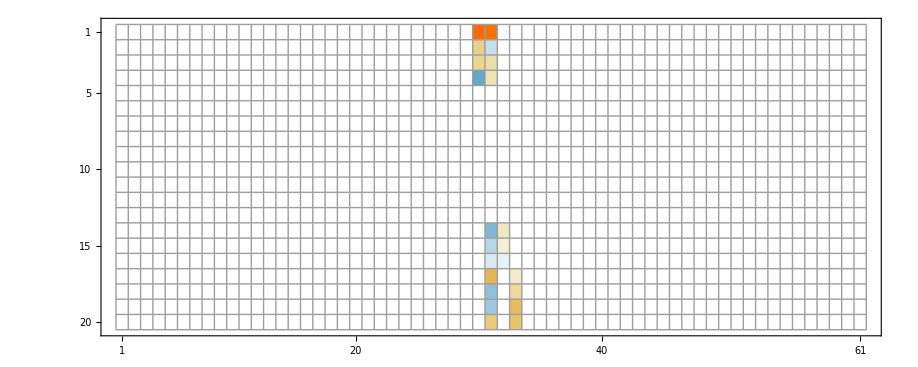

```mathematica
ContributionChart=MatrixPlot[Partition[Flatten[S]*Flatten[DW],61],Mesh->All]
```

```mathematica
SNRContribution=Partition[Flatten[S]*Flatten[DW],61];
SNRContribution//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.70708 | 2.54842 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.220409 | -0.0851782 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.183167 | 0.136561 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.468501 | 0.108728 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.272083 | 0.103813 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.106967 | 0.00581309 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.0286575 | -0.0244856 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.327059 | 0. | 0.0768397 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.244751 | 0. | 0.142449 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.236692 | 0. | 0.316577 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.222791 | 0. | 0.281211 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
Max2
```

0.2688

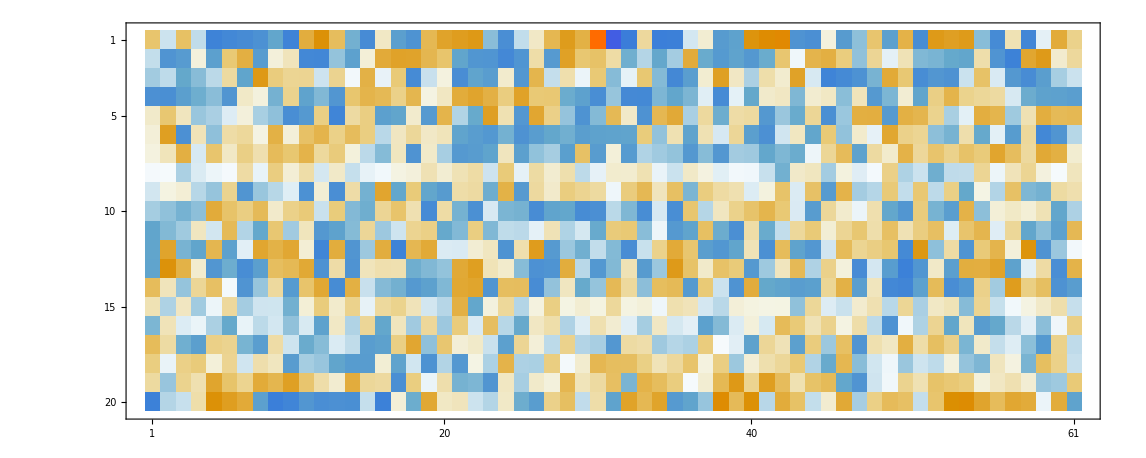

```mathematica
MatrixPlot[DW]
```

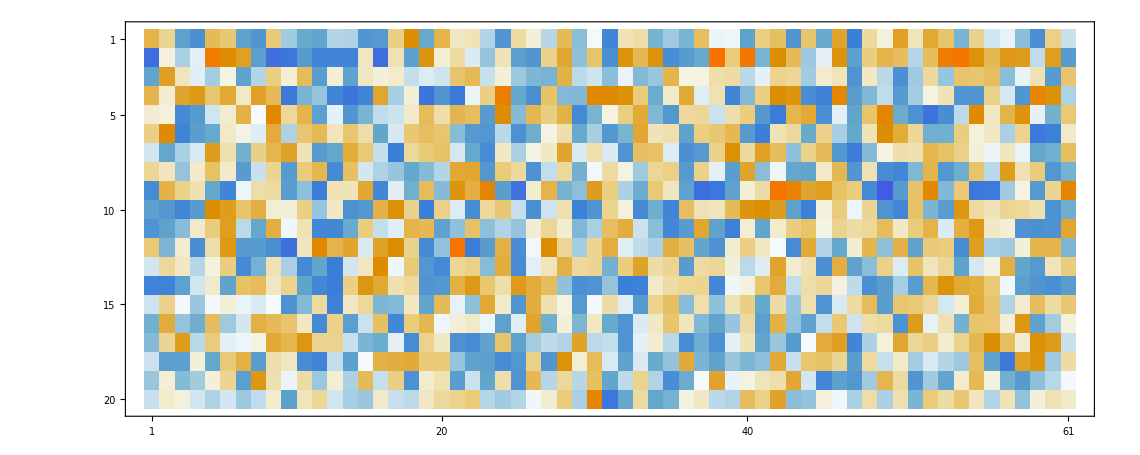

```mathematica
MatrixPlot[BiasData]
```

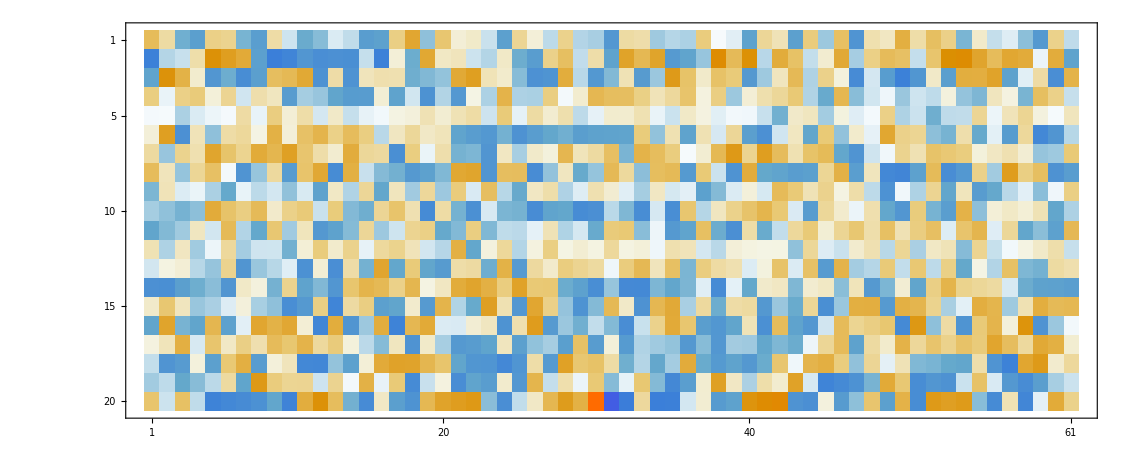

```mathematica
MatrixPlot[Data]
```

```mathematica
Total[Flatten[S]*Flatten[DW]]
```

5.91361

```mathematica
Max[DW]
Min[DW]
```

2.70708

-2.54842

```mathematica
Mean[Mean[Abs[DW]]]
```

0.195624

```mathematica
Max[Max[DW],Abs[Min[DW]]]
```

2.70708

```mathematica
newArray=Transpose[Transpose[DW][[Start;;Finish]]];
```

```mathematica
newArray//MatrixForm
```

(2.70708 | -2.54842 | -1.02064 | 0.104151
0.220409 | 0.0851782 | -0.173698 | -0.0686283
0.183167 | -0.136561 | -0.0167096 | 0.190491
-0.468501 | -0.108728 | -0.557397 | -0.580249
-0.137606 | 0.276049 | 0.0377615 | -0.388307
-0.224718 | -0.222666 | -0.21636 | 0.167165
-0.28299 | 0.0149174 | -0.292985 | -0.0751246
-0.0173525 | 0.0300317 | 0.029975 | 0.0665663
0.0954244 | -0.00695809 | 0.163855 | 0.280401
-0.453893 | -0.0616091 | -0.142901 | -0.479376
-0.186487 | 0.167854 | 0.185608 | -0.129623
-0.0519435 | -0.139024 | -0.472134 | -0.0447182
-0.323516 | -0.140578 | 0.0622011 | -0.29053
-0.111609 | 0.272083 | 0.103813 | -0.124233
0.00538917 | 0.106967 | 0.00581309 | 0.0146584
0.0678362 | 0.0286575 | -0.0244856 | -0.0882789
-0.0853655 | -0.327059 | 0.0899619 | 0.0768397
0.283249 | 0.244751 | 0.24228 | 0.142449
0.0947003 | 0.236692 | -0.151547 | 0.316577
0.0778409 | -0.222791 | 0.493198 | 0.281211)

```mathematica
Max[Max[newArray],Abs[Min[newArray]]]
```

2.70708

```mathematica
Mean[Abs[Flatten[newArray]]]
```

0.24812

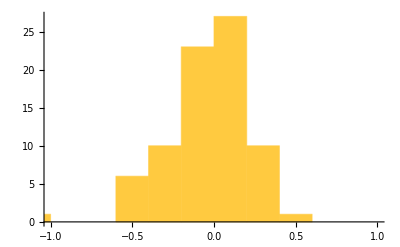

```mathematica
Histogram[Flatten[newArray]]
```

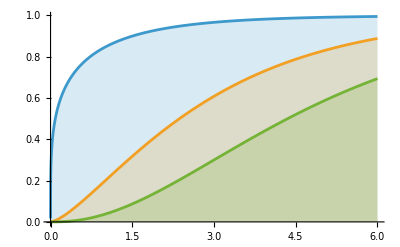

```mathematica
Plot[Table[CDF[ChiSquareDistribution[ν],x],{ν,{0.5,3,5}}]//Evaluate,{x,0,6},Filling->Axis]
```

```mathematica
dist=ChiSquareDistribution[79];
xValue=Quantile[dist,1-5.802891933*10^-7]
```

155.823

```mathematica
Dimensions[Einv]
```

{1220,1220}

```mathematica
NumClocks=Length[Template]
JW=61;
NewJW=Finish-Start+1
NewSize=NumClocks*NewJW
ETrimmed=ConstantArray[0,{NewSize,NewSize}];
```

20

4

80

```mathematica
For[a=0,a<NumClocks,a++,
For[s=1,s<=NewJW,s++,
For[b=0,b<NumClocks,b++,
For[S=1,S<=NewJW,S++,
ETrimmed[[NewJW*b+S,NewJW*a+s]]=Eij[[JW*b+S-1+Start,JW*a+s-1+Start]];
];
];
];
];
```

```mathematica
ETrimmedinv=Inverse[ETrimmed]
```

```mathematica
Dimensions[ETrimmedinv]
```

{80,80}

```mathematica
SNRContributionTrimmed=Transpose[Transpose[SNRContribution][[Start;;Finish]]];
SNRContributionTrimmed//MatrixForm
newArray//MatrixForm
```

(2.70708 | 2.54842 | 0. | 0.
0.220409 | -0.0851782 | 0. | 0.
0.183167 | 0.136561 | 0. | 0.
-0.468501 | 0.108728 | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | -0.272083 | 0.103813 | 0.
0. | -0.106967 | 0.00581309 | 0.
0. | -0.0286575 | -0.0244856 | 0.
0. | 0.327059 | 0. | 0.0768397
0. | -0.244751 | 0. | 0.142449
0. | -0.236692 | 0. | 0.316577
0. | 0.222791 | 0. | 0.281211)

(2.70708 | -2.54842 | -1.02064 | 0.104151
0.220409 | 0.0851782 | -0.173698 | -0.0686283
0.183167 | -0.136561 | -0.0167096 | 0.190491
-0.468501 | -0.108728 | -0.557397 | -0.580249
-0.137606 | 0.276049 | 0.0377615 | -0.388307
-0.224718 | -0.222666 | -0.21636 | 0.167165
-0.28299 | 0.0149174 | -0.292985 | -0.0751246
-0.0173525 | 0.0300317 | 0.029975 | 0.0665663
0.0954244 | -0.00695809 | 0.163855 | 0.280401
-0.453893 | -0.0616091 | -0.142901 | -0.479376
-0.186487 | 0.167854 | 0.185608 | -0.129623
-0.0519435 | -0.139024 | -0.472134 | -0.0447182
-0.323516 | -0.140578 | 0.0622011 | -0.29053
-0.111609 | 0.272083 | 0.103813 | -0.124233
0.00538917 | 0.106967 | 0.00581309 | 0.0146584
0.0678362 | 0.0286575 | -0.0244856 | -0.0882789
-0.0853655 | -0.327059 | 0.0899619 | 0.0768397
0.283249 | 0.244751 | 0.24228 | 0.142449
0.0947003 | 0.236692 | -0.151547 | 0.316577
0.0778409 | -0.222791 | 0.493198 | 0.281211)

```mathematica
DmS=Flatten[Transpose[Transpose[BiasData][[Start;;Finish]]]-h*Transpose[Transpose[Template][[Start;;Finish]]]];
```

```mathematica
Transpose[DmS].ETrimmedinv.DmS
```

110.279

```mathematica
Transpose[Flatten[BiasData-h*Template]].Einv.Flatten[BiasData-h*Template]
```

1375.21

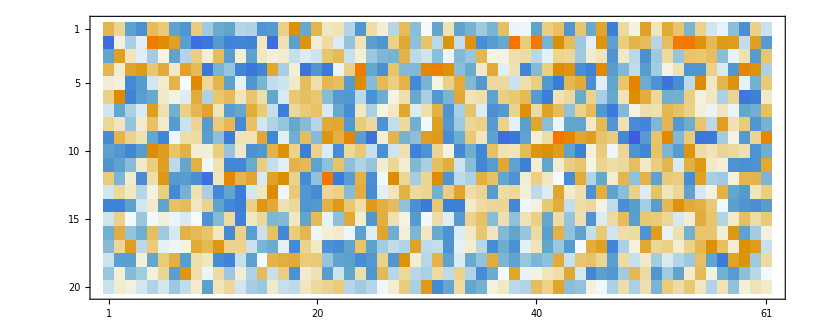

```mathematica
MatrixPlot[(BiasData-h*Template)]
```

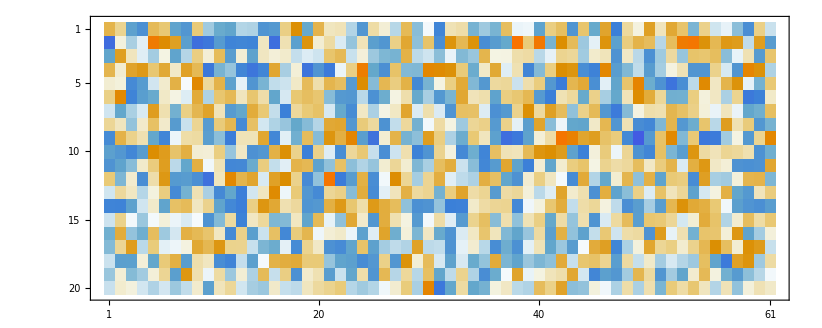

```mathematica
MatrixPlot[BiasData]
```

```mathematica
ChiContribution=Partition[Flatten[BiasData-h*Template]*Flatten[Einv.Flatten[BiasData-h*Template]],61];
```

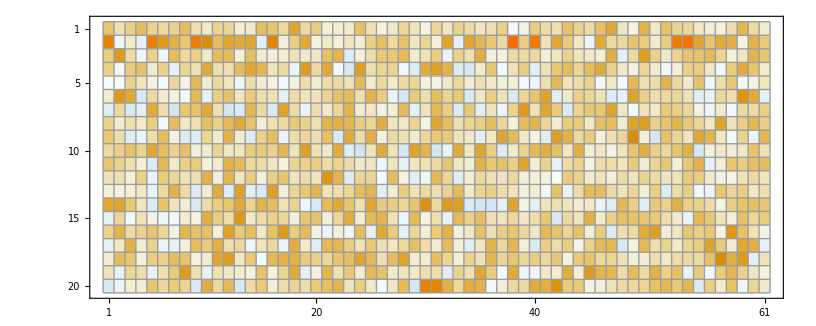

```mathematica
MatrixPlot[ChiContribution,Mesh->All]
```

```mathematica
Transpose[Transpose[ChiContribution][[Start;;Finish]]]//MatrixForm
```

(0.00110838 | 0.54479 | 0.129171 | 0.654851
0.539704 | 0.0390975 | 4.93522 | -0.0361722
0.20181 | 0.810976 | -0.0150153 | 0.68735
4.0138 | 5.6435 | 2.59163 | -0.119857
0.00828787 | 0.000773227 | 0.107575 | 0.422025
0.298881 | 1.75753 | 0.573318 | 1.12317
0.189779 | 2.10944 | 0.799255 | -0.135004
0.00125785 | 4.52226 | 1.79256 | 0.237346
0.466962 | 1.03894 | 1.00905 | 0.173572
2.53982 | -0.348235 | -0.0220521 | 4.00678
0.220422 | 0.362108 | 1.22597 | 0.125072
-0.00682638 | 2.0563 | 0.523446 | -0.0605601
0.3976 | 0.264071 | 0.604715 | 2.00956
8.72922 | 0.381219 | 6.67876 | 5.82389
0.00319793 | 0.275526 | -0.0209234 | 1.91552
0.0387345 | 0.999282 | 2.96918 | 0.00719368
0.319924 | 0.0626053 | 1.77108 | 0.0218631
0.0743719 | 1.66527 | 0.535623 | 0.0253826
0.269678 | 0.306992 | -0.0624809 | 0.600518
14.9268 | 14.1167 | 3.07331 | 0.458471)

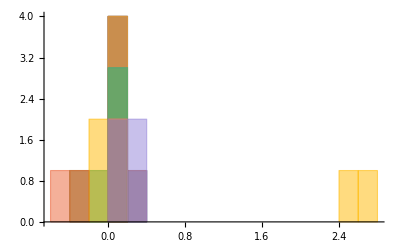

```mathematica
Histogram[SNRContributionTrimmed]
```